```mathematica
starttime=60.0;endtime=240.0;startPitchFl=60.5;startPitchBcl=48.;startPitchVla=60.86313713864835;endPitchFl=67.;endPitchBcl=66.;endPitchVla=66.68825906469125
```

66.6883

```mathematica
fl[x_,startpitch_,endpitch_]:=Sin[Pi/2.0/(endtime-starttime)*(x-starttime)]*(endpitch-startpitch)+startpitch
```

```mathematica
bcl[x_,startpitch_,endpitch_]:=(((x - starttime)/(endtime-starttime)))*(endpitch-startpitch)+startpitch
```

```mathematica
vla[x_,startpitch_,endpitch_]:=(Cos[(x-starttime)*((Pi/2.0)/(endtime-starttime))+Pi]+1)*(endpitch-startpitch)+startpitch
```

```mathematica
f[func_,x_,a_,b_,phi_,startpitch_,endpitch_]:=func[x,startpitch,endpitch]+Sin[(2Pi)/a*(x-starttime)+phi]*b
```

```mathematica
Manipulate[Plot[
{
f[fl,x,a1,b1,0,startPitchFl, endPitchFl],
f[bcl,x,a2,b2,Pi,startPitchBcl,endPitchBcl],
f[vla,x,a3,b3,0,startPitchVla,endPitchVla]
},{x,starttime,endtime},PlotRange->{{0,endtime},{ymin,ymax}},ImageSize->Large],{{a1,90},0,600},{{a2,180},0,600},{{a3,60},0,600},{{b1,2},0,2},{{b2,2},0,2},{{b3,2},0,2},{{startPitchFl, startPitchFl},0,120},{{startPitchBcl,startPitchBcl},0,120},{{startPitchVla,startPitchVla},0,120},{{endPitchFl, endPitchFl},0,120},{{endPitchBcl,endPitchBcl},0,120},{{endPitchVla,endPitchVla},0,120},{{ymin,0},-10,0},{{ymax,84},10,84}]
```

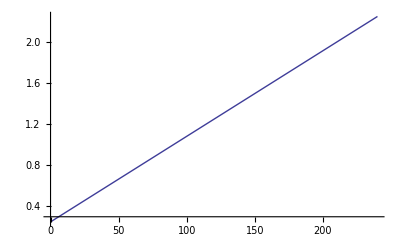

```mathematica
Plot[(((x - starttime)/(endtime-starttime)))*(2.25-.75)+.75,{x,0,endtime}]
```

```mathematica
line[x_,numperiods_]:=(((x - starttime)/(endtime-starttime)))*((.75+numperiods)-.75)+.75
```

```mathematica
Manipulate[{line[x,2.5],RandomVariate[BetaDistribution[((Sin[line[x,2.5]*2Pi]*.5)+.5)*18+2,((Sin[line[x,2.5]*2Pi]*-.5)+.5)*18+2]]},{x,starttime,endtime}]
```

```mathematica
Manipulate[{
{"Fl",f[fl,x,90,2,0,startPitchFl,endPitchFl],RandomVariate[BetaDistribution[((Sin[line[x,2.5]*2Pi]*.5)+.5)*18+2,((Sin[line[x,2.5]*2Pi]*-.5)+.5)*18+2]]},
{"BCl",f[bcl,x,180,2,Pi,startPitchBcl,endPitchBcl],RandomVariate[BetaDistribution[((Sin[line[x,3.5]*2Pi]*.5)+.5)*18+2,((Sin[line[x,2.5]*2Pi]*-.5)+.5)*18+2]]},{"Vla",f[vla,x,60,2,0,startPitchVla,endPitchVla],RandomVariate[BetaDistribution[((Sin[line[x,4.5]*2Pi]*.5)+.5)*18+2,((Sin[line[x,2.5]*2Pi]*-.5)+.5)*18+2]]}},{x,starttime,240}]
```